```mathematica
TheSize=5;
```

```mathematica
allGraphs=Association[];
g=Graph[Range[TheSize],{1<->2,2<->3,3<->4,4<->5,5<->1}];
```

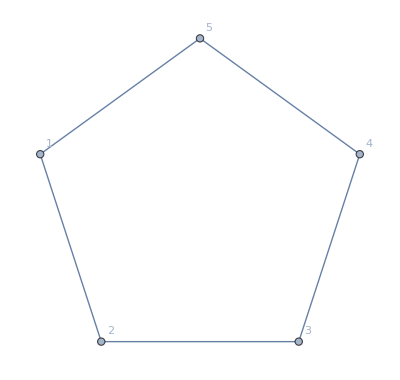

```mathematica
Graph[g,VertexLabels->"Name"]
```

```mathematica
mat = MatrixFromGraph[g]
```

{{2,1,0,0,1},{1,2,1,0,0},{0,1,2,1,0},{0,0,1,2,1},{1,0,0,1,2}}

```mathematica
MatrixForm[mat]
```

(2 | 1 | 0 | 0 | 1
1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2)

```mathematica
FileName="d:\\Saved\\allGraphs"<>ToString[TheSize]<>".m";
If[FileExistsQ[FileName],
Print["Loading ... ", FileName];
allGraphs=Get[FileName],
Timing[Monitor[ComputeGraph[mat,32],{globalDepth,Length[allGraphs]}]];
Put[allGraphs,FileName]
];
Length[allGraphs]
```

57

```mathematica
TableForm[Sort[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,Keys[allGraphs]]//Tally],TableDepth->2]
```

{3,GreaterEqual} | 5
{4,Greater} | 5
{4,GreaterEqual} | 15
{5,Equal} | 1
{5,Greater} | 16
{5,GreaterEqual} | 15

```mathematica
atomKeys=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[atomKeys]
```

11

```mathematica
TableForm[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,atomKeys]//Tally//Sort,TableDepth->2]
```

{3,GreaterEqual} | 5
{4,GreaterEqual} | 5
{5,Equal} | 1